# SU(3) numerical in 1+2 D and gauge field is a function of time only

```mathematica
coord={t,x,y};
n=3;(*# of spacetime dimensions*)
```

```mathematica
(*Minkowski*)
```

```mathematica
gdd={{-1,0,0},{0,1,0},{0,0,1}};
gUU= {{-1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
(*Christoffel  symbols*)
```

```mathematica
ΓUdd=Table[1/2 Sum[gUU[[i]][[l]](D[gdd[[l]][[k]],coord[[j]]]+D[gdd[[l]][[j]],coord[[k]]]-D[ gdd[[j]][[k]],coord[[l]]]),{l,1,n}],{i,1,n},{j,1,n},{k,1,n}];
```

```mathematica
(*Gellmann matrices*)
```

```mathematica
nn=3;(* for SU(N),nn=N*)
λ1={SparseArray[{{1,2}->1,{2,1}->1,{3,3}->0}]};
λ2={SparseArray[{{1,2}->-I,{2,1}->I,{3,3}->0}]};
λ3={SparseArray[{{1,1}->1,{2,2}->-1,{3,3}->0}]};
λ4={SparseArray[{{1,3}->1,{3,1}->1,{3,3}->0}]};
λ5={SparseArray[{{1,3}->-I,{3,1}->I,{3,3}->0}]};λ6={SparseArray[{{2,3}->1,{3,2}->1,{3,3}->0}]};
λ7={SparseArray[{{2,3}->-I,{3,2}->I,{3,3}->0}]};
λ8={1/(√3)SparseArray[{{1,1}->1,{2,2}->1,{3,3}->-2}]};
basis=Join[λ1,λ2,λ3,λ4,λ5,λ6,λ7,λ8];
mat=Normal[basis]
```

{{{0,1,0},{1,0,0},{0,0,0}},{{0,-ⅈ,0},{ⅈ,0,0},{0,0,0}},{{1,0,0},{0,-1,0},{0,0,0}},{{0,0,1},{0,0,0},{1,0,0}},{{0,0,-ⅈ},{0,0,0},{ⅈ,0,0}},{{0,0,0},{0,0,1},{0,1,0}},{{0,0,0},{0,0,-ⅈ},{0,ⅈ,0}},{{1/(√3),0,0},{0,1/(√3),0},{0,0,-2/(√3)}}}

```mathematica
(*Structure constants for SU(3)*)
```

```mathematica
fabc=Table[-I/4 Tr[(mat[[i]].mat[[j]]-mat[[j]].mat[[i]]).ConjugateTranspose[mat[[k]]]],{i,1,8},{j,1,8},{k,1,8}];
```

```mathematica
m=8;(*# of internal indices (SU(3))*)
```

```mathematica
(*Gauge field A with 'a' as internal index and d as spacetime index= Aad*)
```

```mathematica
(*All the combinations in selecting 3 numbers from 1 to 8 numbers*)
```

```mathematica
s=Table[{a,b,c},{a,1,8},{b,1,8},{c,1,8}];
```

```mathematica
s1=Flatten[s,2];
```

```mathematica
(*Making the set with equal numbers to zero*)
```

```mathematica
s2=Table[If[s1[[i]][[1]]==s1[[i]][[2]]||s1[[i]][[1]]==s1[[i]][[3]],0,If[s1[[i]][[2]]==s1[[i]][[3]],0, s1[[i]]]],{i,1,Length[s1]}];
```

```mathematica
s3=DeleteCases[s2,0];
```

```mathematica
(*Making the elements in set in ascending order*)
```

```mathematica
s4=Table[Sort[s3[[i]]],{i,1,Length[s3]}];
```

```mathematica
(*Removing the sets with same elements*)
```

```mathematica
s5=DeleteDuplicates[s4]
```

{{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,2,8},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,3,8},{1,4,5},{1,4,6},{1,4,7},{1,4,8},{1,5,6},{1,5,7},{1,5,8},{1,6,7},{1,6,8},{1,7,8},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,3,8},{2,4,5},{2,4,6},{2,4,7},{2,4,8},{2,5,6},{2,5,7},{2,5,8},{2,6,7},{2,6,8},{2,7,8},{3,4,5},{3,4,6},{3,4,7},{3,4,8},{3,5,6},{3,5,7},{3,5,8},{3,6,7},{3,6,8},{3,7,8},{4,5,6},{4,5,7},{4,5,8},{4,6,7},{4,6,8},{4,7,8},{5,6,7},{5,6,8},{5,7,8},{6,7,8}}

```mathematica
(*These are total 56 unique combinations*)
```

```mathematica
(*Ap=set containing nonzero elements, Ag=the guage field for a single combination*)
```

```mathematica
Ap={{0,0,ϕ,0},{0,ψ,0,0},{ξ,0,0,m3 ξ}};Ag=ConstantArray[0,{8,4}];
```

```mathematica
(*Agg=Matric containing the gauge field ansatzs for all combinations*)
```

```mathematica
Agg=ConstantArray[0,{56,8,4}];
```

```mathematica
For[k=1,k<57,k++,Ag=ConstantArray[0,{8,4}];For[i=1,i<9,i++,For[j=1,j<4,j++,If[s5[[k]][[j]]==i,Ag[[i]]=Ap[[j]];Break[],Continue[]]]];Agg[[k]]=Ag]
```

```mathematica
(*In Hamiton gauge, Subscript[A, 0]^a=0*)
```

```mathematica
Aad={{0,Subscript[A, 1,1][t],Subscript[A, 1,2][t]},{0,Subscript[A, 2,1][t],Subscript[A, 2,2][t]},{0,Subscript[A, 3,1][t],Subscript[A, 3,2][t]},{0,Subscript[A, 4,1][t],Subscript[A, 4,2][t]},{0,Subscript[A, 5,1][t],Subscript[A, 5,2][t]},{0,Subscript[A, 6,1][t],Subscript[A, 6,2][t]},{0,Subscript[A, 7,1][t],Subscript[A, 7,2][t]},{0,Subscript[A, 8,1][t],Subscript[A, 8,2][t]}}
```

{{0,A_(1,1)[t],A_(1,2)[t]},{0,A_(2,1)[t],A_(2,2)[t]},{0,A_(3,1)[t],A_(3,2)[t]},{0,A_(4,1)[t],A_(4,2)[t]},{0,A_(5,1)[t],A_(5,2)[t]},{0,A_(6,1)[t],A_(6,2)[t]},{0,A_(7,1)[t],A_(7,2)[t]},{0,A_(8,1)[t],A_(8,2)[t]}}

```mathematica
Aad//MatrixForm
```

(0 | A_(1,1)[t] | A_(1,2)[t]
0 | A_(2,1)[t] | A_(2,2)[t]
0 | A_(3,1)[t] | A_(3,2)[t]
0 | A_(4,1)[t] | A_(4,2)[t]
0 | A_(5,1)[t] | A_(5,2)[t]
0 | A_(6,1)[t] | A_(6,2)[t]
0 | A_(7,1)[t] | A_(7,2)[t]
0 | A_(8,1)[t] | A_(8,2)[t])

```mathematica
(*Field strength tensor(Subscript[F, μν])*)
```

```mathematica
Fadd=Table[D[Aad[[a]][[j]],coord[[i]]]- D[Aad[[a]][[i]],coord[[j]]] +g Sum[fabc[[a]][[b]][[c]] Aad[[b]][[i]]Aad[[c]][[j]],{b,1,m},{c,1,m}],{a,1,m},{i,1,n},{j,1,n}];
```

```mathematica
(*F^μν*)
```

```mathematica
FaUU=Table[Sum[gUU[[i]][[k]]gUU[[j]][[l]]Fadd[[a]][[k]][[l]],{k,1,n},{l,1,n}],{a,1,m},{i,1,n},{j,1,n}];
```

```mathematica
(*∇_μ F^μν*)
```

```mathematica
CovDFaUU=Table[Sum[D[FaUU[[a]][[k]][[j]],coord[[k]]] +Sum[ ΓUdd[[k]][[k]][[l]] FaUU[[a]][[l]][[j]] + ΓUdd[[j]][[k]][[l]]FaUU[[a]][[k]][[l]],{l,1,n}] ,{k,1,n}],{a,1,m},{j,1,n}];
```

```mathematica
(*g Subscript[f, abc] Subscript[A, μ]^b F^cμν*)
```

```mathematica
NonaU=Table[Sum[g fabc[[a]][[b]][[c]] Aad[[b]][[i]] FaUU[[c]][[i]][[j]],{b,1,m},{c,1,m},{i,1,n}],{a,1,m},{j,1,n}];
```

```mathematica
(*∇_μ F^μν+g Subscript[f, abc] Subscript[A, μ]^b F^cμν*)
```

```mathematica
YMeq=CovDFaUU+NonaU;
```

```mathematica
YMeq[[1]]//MatrixForm
```

(-g A_(3,1)[t] A_(2,1)'[t]-g A_(3,2)[t] A_(2,2)'[t]+g A_(2,1)[t] A_(3,1)'[t]+g A_(2,2)[t] A_(3,2)'[t]-1/2 g A_(7,1)[t] A_(4,1)'[t]-1/2 g A_(7,2)[t] A_(4,2)'[t]+1/2 g A_(6,1)[t] A_(5,1)'[t]+1/2 g A_(6,2)[t] A_(5,2)'[t]-1/2 g A_(5,1)[t] A_(6,1)'[t]-1/2 g A_(5,2)[t] A_(6,2)'[t]+1/2 g A_(4,1)[t] A_(7,1)'[t]+1/2 g A_(4,2)[t] A_(7,2)'[t]
-g^2 A_(3,2)[t] (-A_(1,2)[t] A_(3,1)[t]+A_(1,1)[t] A_(3,2)[t]+1/2 A_(4,2)[t] A_(6,1)[t]-1/2 A_(4,1)[t] A_(6,2)[t]+1/2 A_(5,2)[t] A_(7,1)[t]-1/2 A_(5,1)[t] A_(7,2)[t])+g^2 A_(2,2)[t] (A_(1,2)[t] A_(2,1)[t]-A_(1,1)[t] A_(2,2)[t]+1/2 A_(4,2)[t] A_(5,1)[t]-1/2 A_(4,1)[t] A_(5,2)[t]-1/2 A_(6,2)[t] A_(7,1)[t]+1/2 A_(6,1)[t] A_(7,2)[t])+1/2 g^2 A_(6,2)[t] (1/2 A_(3,2)[t] A_(4,1)[t]-1/2 A_(3,1)[t] A_(4,2)[t]+1/2 A_(1,2)[t] A_(6,1)[t]-1/2 A_(1,1)[t] A_(6,2)[t]-1/2 A_(2,2)[t] A_(7,1)[t]+1/2 A_(2,1)[t] A_(7,2)[t]-1/2 √3 A_(4,2)[t] A_(8,1)[t]+1/2 √3 A_(4,1)[t] A_(8,2)[t])-1/2 g^2 A_(7,2)[t] (-1/2 A_(3,2)[t] A_(5,1)[t]+1/2 A_(3,1)[t] A_(5,2)[t]-1/2 A_(2,2)[t] A_(6,1)[t]+1/2 A_(2,1)[t] A_(6,2)[t]-1/2 A_(1,2)[t] A_(7,1)[t]+1/2 A_(1,1)[t] A_(7,2)[t]+1/2 √3 A_(5,2)[t] A_(8,1)[t]-1/2 √3 A_(5,1)[t] A_(8,2)[t])+1/2 g^2 A_(4,2)[t] (1/2 A_(1,2)[t] A_(4,1)[t]-1/2 A_(1,1)[t] A_(4,2)[t]+1/2 A_(2,2)[t] A_(5,1)[t]-1/2 A_(2,1)[t] A_(5,2)[t]-1/2 A_(3,2)[t] A_(6,1)[t]+1/2 A_(3,1)[t] A_(6,2)[t]-1/2 √3 A_(6,2)[t] A_(8,1)[t]+1/2 √3 A_(6,1)[t] A_(8,2)[t])-1/2 g^2 A_(5,2)[t] (1/2 A_(2,2)[t] A_(4,1)[t]-1/2 A_(2,1)[t] A_(4,2)[t]-1/2 A_(1,2)[t] A_(5,1)[t]+1/2 A_(1,1)[t] A_(5,2)[t]+1/2 A_(3,2)[t] A_(7,1)[t]-1/2 A_(3,1)[t] A_(7,2)[t]+1/2 √3 A_(7,2)[t] A_(8,1)[t]-1/2 √3 A_(7,1)[t] A_(8,2)[t])-A_(1,1)''[t]
-g^2 A_(3,1)[t] (A_(1,2)[t] A_(3,1)[t]-A_(1,1)[t] A_(3,2)[t]-1/2 A_(4,2)[t] A_(6,1)[t]+1/2 A_(4,1)[t] A_(6,2)[t]-1/2 A_(5,2)[t] A_(7,1)[t]+1/2 A_(5,1)[t] A_(7,2)[t])+g^2 A_(2,1)[t] (-A_(1,2)[t] A_(2,1)[t]+A_(1,1)[t] A_(2,2)[t]-1/2 A_(4,2)[t] A_(5,1)[t]+1/2 A_(4,1)[t] A_(5,2)[t]+1/2 A_(6,2)[t] A_(7,1)[t]-1/2 A_(6,1)[t] A_(7,2)[t])+1/2 g^2 A_(6,1)[t] (-1/2 A_(3,2)[t] A_(4,1)[t]+1/2 A_(3,1)[t] A_(4,2)[t]-1/2 A_(1,2)[t] A_(6,1)[t]+1/2 A_(1,1)[t] A_(6,2)[t]+1/2 A_(2,2)[t] A_(7,1)[t]-1/2 A_(2,1)[t] A_(7,2)[t]+1/2 √3 A_(4,2)[t] A_(8,1)[t]-1/2 √3 A_(4,1)[t] A_(8,2)[t])-1/2 g^2 A_(7,1)[t] (1/2 A_(3,2)[t] A_(5,1)[t]-1/2 A_(3,1)[t] A_(5,2)[t]+1/2 A_(2,2)[t] A_(6,1)[t]-1/2 A_(2,1)[t] A_(6,2)[t]+1/2 A_(1,2)[t] A_(7,1)[t]-1/2 A_(1,1)[t] A_(7,2)[t]-1/2 √3 A_(5,2)[t] A_(8,1)[t]+1/2 √3 A_(5,1)[t] A_(8,2)[t])+1/2 g^2 A_(4,1)[t] (-1/2 A_(1,2)[t] A_(4,1)[t]+1/2 A_(1,1)[t] A_(4,2)[t]-1/2 A_(2,2)[t] A_(5,1)[t]+1/2 A_(2,1)[t] A_(5,2)[t]+1/2 A_(3,2)[t] A_(6,1)[t]-1/2 A_(3,1)[t] A_(6,2)[t]+1/2 √3 A_(6,2)[t] A_(8,1)[t]-1/2 √3 A_(6,1)[t] A_(8,2)[t])-1/2 g^2 A_(5,1)[t] (-1/2 A_(2,2)[t] A_(4,1)[t]+1/2 A_(2,1)[t] A_(4,2)[t]+1/2 A_(1,2)[t] A_(5,1)[t]-1/2 A_(1,1)[t] A_(5,2)[t]-1/2 A_(3,2)[t] A_(7,1)[t]+1/2 A_(3,1)[t] A_(7,2)[t]-1/2 √3 A_(7,2)[t] A_(8,1)[t]+1/2 √3 A_(7,1)[t] A_(8,2)[t])-A_(1,2)''[t])

```mathematica
YMeq[[1]][[1]]/.{Subscript[A, a_,b_]'[t]->Subscript[P, a,b][t]}
```

-0.5 A_(3,1)[t] P_(2,1)[t]-0.5 A_(3,2)[t] P_(2,2)[t]+0.5 A_(2,1)[t] P_(3,1)[t]+0.5 A_(2,2)[t] P_(3,2)[t]-0.25 A_(7,1)[t] P_(4,1)[t]-0.25 A_(7,2)[t] P_(4,2)[t]+0.25 A_(6,1)[t] P_(5,1)[t]+0.25 A_(6,2)[t] P_(5,2)[t]-0.25 A_(5,1)[t] P_(6,1)[t]-0.25 A_(5,2)[t] P_(6,2)[t]+0.25 A_(4,1)[t] P_(7,1)[t]+0.25 A_(4,2)[t] P_(7,2)[t]

## Hamiltonian Procedure

```mathematica
A[t_]=Table[Subscript[A, i,j][t],{i,1,m},{j,1,2}]
```

{{A_(1,1)[t],A_(1,2)[t]},{A_(2,1)[t],A_(2,2)[t]},{A_(3,1)[t],A_(3,2)[t]},{A_(4,1)[t],A_(4,2)[t]},{A_(5,1)[t],A_(5,2)[t]},{A_(6,1)[t],A_(6,2)[t]},{A_(7,1)[t],A_(7,2)[t]},{A_(8,1)[t],A_(8,2)[t]}}

```mathematica
P[t_]=Table[Subscript[P, i,j][t],{i,1,m},{j,1,2}]
```

{{P_(1,1)[t],P_(1,2)[t]},{P_(2,1)[t],P_(2,2)[t]},{P_(3,1)[t],P_(3,2)[t]},{P_(4,1)[t],P_(4,2)[t]},{P_(5,1)[t],P_(5,2)[t]},{P_(6,1)[t],P_(6,2)[t]},{P_(7,1)[t],P_(7,2)[t]},{P_(8,1)[t],P_(8,2)[t]}}

```mathematica
g=0.5;
```

```mathematica
eqns=Join[Flatten[Table[D[P[t],t][[i]][[j]]==-YMeq[[i]][[j+1]]-D[A[t],t,t][[i]][[j]],{i,1,m},{j,1,2}]],Flatten[Table[D[A[t],t][[i]][[j]]==P[t][[i]][[j]],{i,1,m},{j,1,2}]]];
```

```mathematica
ics={Subscript[A, 1,1][0]==0.2,Subscript[A, 1,2][0]==0,Subscript[A, 2,1][0]==0.1,Subscript[A, 2,2][0]==0.1,Subscript[A, 3,1][0]==0,Subscript[A, 3,2][0]==.1,Subscript[A, 4,1][0]==0.2,Subscript[A, 4,2][0]==0,Subscript[A, 5,1][0]==0.1,Subscript[A, 5,2][0]==0.1,Subscript[A, 6,1][0]==0,Subscript[A, 6,2][0]==.1,Subscript[A, 7,1][0]==0.2,Subscript[A, 7,2][0]==0,Subscript[A, 8,1][0]==0.1,Subscript[A, 8,2][0]==0.1,
Subscript[P, 1,1][0]==0,Subscript[P, 1,2][0]==0,Subscript[P, 2,1][0]==0,Subscript[P, 2,2][0]==.1,Subscript[P, 3,1][0]==0,Subscript[P, 3,2][0]==0.1,Subscript[P, 4,1][0]==0,Subscript[P, 4,2][0]==0,Subscript[P, 5,1][0]==0,Subscript[P, 5,2][0]==.1,Subscript[P, 6,1][0]==0,Subscript[P, 6,2][0]==0.1,Subscript[P, 7,1][0]==0,Subscript[P, 7,2][0]==0,Subscript[P, 8,1][0]==0,Subscript[P, 8,2][0]==.1};
```

```mathematica
vars=Flatten[Join[A[t],P[t]]];
```

```mathematica
sol=NDSolve[{eqns,ics},vars,{t,0,10},Method->"StiffnessSwitching",MaxStepSize->0.1]
```

NDSolve::ndsz: At t == 8.44847, step size is effectively zero; singularity or stiff system suspected.

{{A_(1,1)[t]→InterpolatingFunction[…][t],A_(1,2)[t]→InterpolatingFunction[…][t],A_(2,1)[t]→InterpolatingFunction[…][t],A_(2,2)[t]→InterpolatingFunction[…][t],A_(3,1)[t]→InterpolatingFunction[…][t],A_(3,2)[t]→InterpolatingFunction[…][t],A_(4,1)[t]→InterpolatingFunction[…][t],A_(4,2)[t]→InterpolatingFunction[…][t],A_(5,1)[t]→InterpolatingFunction[…][t],A_(5,2)[t]→InterpolatingFunction[…][t],A_(6,1)[t]→InterpolatingFunction[…][t],A_(6,2)[t]→InterpolatingFunction[…][t],A_(7,1)[t]→InterpolatingFunction[…][t],A_(7,2)[t]→InterpolatingFunction[…][t],A_(8,1)[t]→InterpolatingFunction[…][t],A_(8,2)[t]→InterpolatingFunction[…][t],P_(1,1)[t]→InterpolatingFunction[…][t],P_(1,2)[t]→InterpolatingFunction[…][t],P_(2,1)[t]→InterpolatingFunction[…][t],P_(2,2)[t]→InterpolatingFunction[…][t],P_(3,1)[t]→InterpolatingFunction[…][t],P_(3,2)[t]→InterpolatingFunction[…][t],P_(4,1)[t]→InterpolatingFunction[…][t],P_(4,2)[t]→InterpolatingFunction[…][t],P_(5,1)[t]→InterpolatingFunction[…][t],P_(5,2)[t]→InterpolatingFunction[…][t],P_(6,1)[t]→InterpolatingFunction[…][t],P_(6,2)[t]→InterpolatingFunction[…][t],P_(7,1)[t]→InterpolatingFunction[…][t],P_(7,2)[t]→InterpolatingFunction[…][t],P_(8,1)[t]→InterpolatingFunction[…][t],P_(8,2)[t]→InterpolatingFunction[…][t]}}

```mathematica
sol=NDSolve[{eqns,ics},vars,{t,0,20},Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->2,"PositionVariables"->Flatten[A[t]]},StartingStepSize->0.2]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

NDSolve::nlnum1: The function value {Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],«6»} is not a list of numbers with dimensions {16} when the arguments are {14.8,9.62056010863767`15.954589770191005*^743148923535705,-2.134739244175419`15.954589770191005*^743148923535705,3.190762577985235`15.954589770191005*^743148923535705,7.738373542546045`15.954589770191005*^743148923535705,-7.940328438410881`15.954589770191005*^743148923535704,6.112082286826397`15.954589770191005*^743148923535705,2.642568874451667`15.954589770191005*^743148923535705,6.224941761437776`15.954589770191005*^743148923535704,-1.850537754681622`15.954589770191005*^743148923535705,«7»}.

{{A_(1,1)[t]→InterpolatingFunction[…][t],A_(1,2)[t]→InterpolatingFunction[…][t],A_(2,1)[t]→InterpolatingFunction[…][t],A_(2,2)[t]→InterpolatingFunction[…][t],A_(3,1)[t]→InterpolatingFunction[…][t],A_(3,2)[t]→InterpolatingFunction[…][t],A_(4,1)[t]→InterpolatingFunction[…][t],A_(4,2)[t]→InterpolatingFunction[…][t],A_(5,1)[t]→InterpolatingFunction[…][t],A_(5,2)[t]→InterpolatingFunction[…][t],A_(6,1)[t]→InterpolatingFunction[…][t],A_(6,2)[t]→InterpolatingFunction[…][t],A_(7,1)[t]→InterpolatingFunction[…][t],A_(7,2)[t]→InterpolatingFunction[…][t],A_(8,1)[t]→InterpolatingFunction[…][t],A_(8,2)[t]→InterpolatingFunction[…][t],P_(1,1)[t]→InterpolatingFunction[…][t],P_(1,2)[t]→InterpolatingFunction[…][t],P_(2,1)[t]→InterpolatingFunction[…][t],P_(2,2)[t]→InterpolatingFunction[…][t],P_(3,1)[t]→InterpolatingFunction[…][t],P_(3,2)[t]→InterpolatingFunction[…][t],P_(4,1)[t]→InterpolatingFunction[…][t],P_(4,2)[t]→InterpolatingFunction[…][t],P_(5,1)[t]→InterpolatingFunction[…][t],P_(5,2)[t]→InterpolatingFunction[…][t],P_(6,1)[t]→InterpolatingFunction[…][t],P_(6,2)[t]→InterpolatingFunction[…][t],P_(7,1)[t]→InterpolatingFunction[…][t],P_(7,2)[t]→InterpolatingFunction[…][t],P_(8,1)[t]→InterpolatingFunction[…][t],P_(8,2)[t]→InterpolatingFunction[…][t]}}

```mathematica
A11[t_]=Subscript[A, 1,1][t]/.sol[[1]];A12[t_]=Subscript[A, 1,2][t]/.sol[[1]];
A21[t_]=Subscript[A, 2,1][t]/.sol[[1]];A22[t_]=Subscript[A, 2,2][t]/.sol[[1]];
A31[t_]=Subscript[A, 3,1][t]/.sol[[1]] ;A32[t_]=Subscript[A, 3,2][t]/.sol[[1]];
A41[t_]=Subscript[A, 4,1][t]/.sol[[1]];A42[t_]=Subscript[A, 4,2][t]/.sol[[1]];
A51[t_]=Subscript[A, 5,1][t]/.sol[[1]];A52[t_]=Subscript[A, 5,2][t]/.sol[[1]];
A61[t_]=Subscript[A, 6,1][t]/.sol[[1]] ;A62[t_]=Subscript[A, 6,2][t]/.sol[[1]];
A71[t_]=Subscript[A, 7,1][t]/.sol[[1]];A72[t_]=Subscript[A, 7,2][t]/.sol[[1]];
A81[t_]=Subscript[A, 8,1][t]/.sol[[1]];A82[t_]=Subscript[A, 8,2][t]/.sol[[1]];
```

```mathematica
P11[t_]=Subscript[P, 1,1][t]/.sol[[1]];P12[t_]=Subscript[P, 1,2][t]/.sol[[1]];
P21[t_]=Subscript[P, 2,1][t]/.sol[[1]];P22[t_]=Subscript[P, 2,2][t]/.sol[[1]];
P31[t_]=Subscript[P, 3,1][t]/.sol[[1]];P32[t_]=Subscript[P, 3,2][t]/.sol[[1]];
P41[t_]=Subscript[P, 4,1][t]/.sol[[1]];P42[t_]=Subscript[P, 4,2][t]/.sol[[1]];
P51[t_]=Subscript[P, 5,1][t]/.sol[[1]];P52[t_]=Subscript[P, 5,2][t]/.sol[[1]];
P61[t_]=Subscript[P, 6,1][t]/.sol[[1]];P62[t_]=Subscript[P, 6,2][t]/.sol[[1]];
P71[t_]=Subscript[P, 7,1][t]/.sol[[1]];P72[t_]=Subscript[P, 7,2][t]/.sol[[1]];
P81[t_]=Subscript[P, 8,1][t]/.sol[[1]];P82[t_]=Subscript[P, 8,2][t]/.sol[[1]];
```

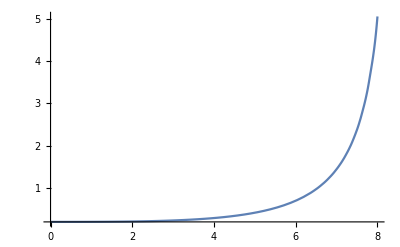

```mathematica
Plot[A11[t],{t,0,8},PlotRange->All]
```

```mathematica
(*Gauss Constraints*)
```

```mathematica
GC1[t_]= YMeq[[1]][[1]]/.{Subscript[A, a_,b_]'[t]->Subscript[P, a,b][t]};
```

```mathematica
GC2[t_]= YMeq[[2]][[1]]/.{Subscript[A, a_,b_]'[t]->Subscript[P, a,b][t]};
```

```mathematica
GC3[t_]= YMeq[[3]][[1]]/.{Subscript[A, a_,b_]'[t]->Subscript[P, a,b][t]};
```

```mathematica
GC11[t_]=-0.5 A11[t] P21[t]-0.5 A32[t] P22[t]+0.5 A21[t] P31[t]+0.5 A22[t] P32[t]-0.25 A71[t] P41[t]-0.25 A72[t] P42[t]+0.25 A61[t] P51[t]+0.25 A62[t] P52[t]-0.25 A51[t] P61[t]-0.25 A52[t] P62[t]+0.25 A41[t]P71[t]+0.25 A42[t] P72[t];
```

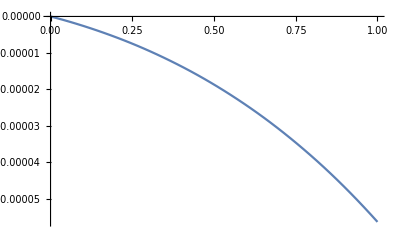

```mathematica
Plot[%173,{t,0,1},PlotRange->All]
```